## Introduction

This notebook was created to help generate the stimuli and analyse the data which will come from injecting Tetradotoxin and Pymetrozine in mosquitos. 
These are important toxins as they perform different types of blocks, which can yield different responses in the nerves. 

We want to better understand the effect of those drugs on the presence of Distortion Products as it could elucidate their roles in audition and audibility.

## Stimuli Generation

### Requirements & Specifications

For this set of experiments we had agreed on the following with Joerg:
• The experiment must be as simple as possible: fixed frequency and fixed amplitude. 
• We want the potential SSO to entrain to the stimulus prior to injection, so stimuli need to be in entrainment regime. 
	We know that depending on amplitude, the entrainment can change dramatically. 
	We want values between 300 - 450 Hz
• It must account for variability in SSO frequency between mosquitoes. 

What I have yet to resolve is the amplitude of stimulation.

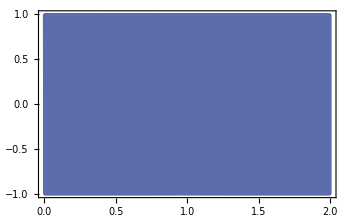

```mathematica
Clear[sinewave]
sinewave::"usage"="

"


Options[sinewave]={
"amp"->1,
"sRate"->20 10^3,
"phase"->0,
"export"->False,
"function"->1.,
"directory"->"C:\\Users\\hadif\\Documents\\"
};
sinewave[freq_,duration_,opts:OptionsPattern[sinewave]]:=Block[{amp,sRate,phase,dir,export,func,nSamples,f,time,ftone,data},
(*
freq: desired frequency on the output, in Hz.
duration: duration of the sinewave, in seconds.
*)

{amp,sRate,phase,export,dir,func}=OptionValue[#]&/@{"amp","sRate","phase","export","directory","function"};

nSamples = Round[duration sRate]                                        (* number of samples *);
f = Round[freq nSamples/sRate]sRate/nSamples;                    (* calculated f *)
time  = Array[#&,nSamples,{0,nSamples/sRate}]; (* time axis generation *)
ftone = amp Cos[ 1. 2π f time + phase];                          (* generate the first frequency *)


(* export the data if instructed to, otherwise, just output the data straight away.*)
If[export,                                               
Export[dir<>"f_"<>ToString[Round[f]]<>"_Hz_sr_"<>ToString[Round[sRate]]<>"_Hz.txt",{{"Time [s]","Amplitude [V]"}}~Join~({1. time,ftone}ᵀ),"CSV"],
{time,ftone}ᵀ
]

]

ListLinePlot[sinewave[200,2]]
```

```mathematica
sinewave[#,2,"export"->True]&/@Range[320,450,5]
```

{C:\Users\hadif\Documents\f_320_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_325_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_330_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_335_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_340_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_345_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_350_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_355_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_360_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_365_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_370_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_375_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_380_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_385_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_390_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_395_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_400_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_405_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_410_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_415_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_420_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_425_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_430_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_435_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_440_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_445_Hz_sr_20000_Hz.txt,C:\Users\hadif\Documents\f_450_Hz_sr_20000_Hz.txt}